```mathematica
(*Lab 12*) 

(*CONSTANTS*) 
t1 = List[];
t0 = 0;
phi = 0.436332313;
mSun = 1.99*10^30;
mEarth = 0; (*original = 5.97*10^24*) 
rES = 1.5*10^11;
rEarth = 6.37*10^6; 
rSun = 6.96*10^8;
vESC =  1.1*10^4; (*original = 1.1*10^4 *) 
SE = 1.5;
omega = 0; (*original = 1.99*10^-7*) 
g = 9.81 ;
G = 6.574*10^-11;
LS = (rES*mEarth)/(mEarth + mSun);
LE = (rES*mSun)/(mEarth + mSun);
v0 = SE*vESC;
v0 = √((G*mSun^2)/(rES*(mSun+mEarth)))
myPath = List[];
```

29532.2

```mathematica
noIter = 0;
While [noIter<1,
	(*SE = RandomReal[{0.7,1.3}];
	(*SE = 0.7; *)
	degPhi = RandomReal[360];
	(*degPhi = 100;*)
	phi = degPhi * π/180;
	v0 = SE*vESC;*)

	(*LIMITS OF INTEGRATION *) 

	deltaT = 1000; 
	tmin = 0;
	t = tmin;
	tmax = 3*365*24*60*60; (* original =  3*365*24*60*60 *) 

(*INITIAL CONDITIONS*) 


	x0 = LE + rEarth*Cos[phi];
	v0X =  v0*Cos[phi];
	x1= x0+ (v0X*deltaT);

	y0 =  rEarth*Sin[phi];
	v0Y = (LE*omega)+  v0*Sin[phi];
	y1 = y0 + (v0Y*deltaT);
	xPROJ = x1;
	yPROJ = y1;
	

	AppendTo[myPath,{x0,y0}];
	AppendTo[myPath,{x1,y1}];
	myPath;
	

	t = deltaT;

	dS = √((xPROJ + LS*Cos[omega*t])^2+ (yPROJ + LS*Sin[omega*t])^2);
	dE = √((xPROJ - LE*Cos[omega*t])^2+ (yPROJ -LE*Sin[omega*t])^2);
	ax = (-(G *mSun)*(xPROJ + LS*Cos[omega*t]))/(dS)^3 + (-(G *mEarth)*(xPROJ- LE*Cos[omega*t]))/(dE)^3;
	ay = (-(G *mSun)*(yPROJ + LS*Sin[omega*t]))/(dS)^3 + (-(G *mEarth)*(yPROJ- LE*Sin[omega*t]))/(dE)^3;

(*START ITERATIONS*) 
	While[t<tmax,
		dS = √((x1 + LS*Cos[omega*t])^2+ (y1 + LS*Sin[omega*t])^2);
		dE = √((x1 - LE*Cos[omega*t])^2+ (y1 -LE*Sin[omega*t])^2);
		a1x = -(G *mSun*(x1 + LS*Cos[omega*t]))/(dS)^3 - (G *mEarth*(x1- LE*Cos[omega*t]))/(dE)^3;
		a1y =-(G *mSun*(y1 + LS*Sin[omega*t]))/(dS)^3 - (G *mEarth*(y1- LE*Sin[omega*t]))/(dE)^3;
	
		xPROJ=2x1- x0 + a1x*deltaT^2;
		yPROJ=2y1- y0 + a1y*deltaT^2;
		AppendTo[myPath,{xPROJ,yPROJ}]; 
		dC = √(xPROJ^2+yPROJ^2);

		If[dS<rSun, Print["SUN HIT"]];
		 If[dS<rSun, dC = -1];
		If[ dS< rSun, Break[]];
		If[dE<rEarth, Print["EARTH HIT"]];
		If[dE<rEarth, dC = -2];
		If[dE < rEarth, Break[]]; 

		x0 = x1;
		x1 = xPROJ;
		y0 = y1; 
		y1 = yPROJ; 
	
	
		t = t + deltaT; ];

	AppendTo[t1, {degPhi, SE, dC}];
	noIter++;
]

t1
```

{{260.401,1.5,1.14935×10^11}}

```mathematica
myPath
```

{{1.50006×10^11,2.69208×10^6},{1.50033×10^11,1.51729×10^7},{1.50059×10^11,2.76538×10^7},{1.50086×10^11,4.01346×10^7},{1.50113×10^11,5.26155×10^7},{1.5014×10^11,6.50963×10^7},{1.50166×10^11,7.75771×10^7},{1.50193×10^11,9.0058×10^7},{1.5022×10^11,1.02539×10^8},{1.50246×10^11,1.1502×10^8},94589,{1.13707×10^11,-1.45171×10^10},{1.13743×10^11,-1.45052×10^10},{1.13779×10^11,-1.44933×10^10},{1.13814×10^11,-1.44814×10^10},{1.1385×10^11,-1.44695×10^10},{1.13885×10^11,-1.44575×10^10},{1.13921×10^11,-1.44456×10^10},{1.13957×10^11,-1.44337×10^10},{1.13992×10^11,-1.44218×10^10},{1.14028×10^11,-1.44098×10^10}}
 |  |  |  |

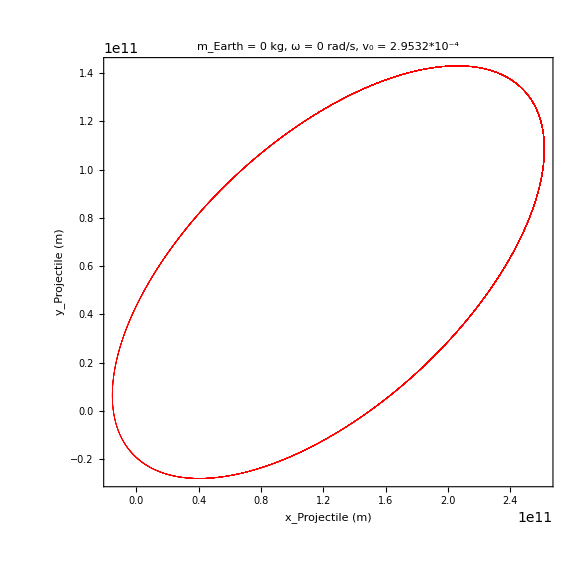

```mathematica
ListPlot[myPath,PlotLabel -> (" m_Earth = 0 kg, ω = 0 rad/s, v_0 = 2.9532*10^-4"),PlotRange->All,ImageSize->Large, Joined->False,Frame->True,FrameLabel->{"x_Projectile (m) ","y_Projectile (m)","",""}, LabelStyle->{FontSize->14, Directive[Bold,Black]},PlotStyle->{RGBColor[1,0,0],PointSize[0.001]},AspectRatio->1]
```

{{351.248,0.776218,1.45759×10^11},{286.695,1.214,1.19921×10^11},{230.775,1.04863,1.30361×10^11},{75.5782,0.925296,2.23868×10^11},{308.005,1.23388,1.58697×10^11},{279.963,1.28837,1.44425×10^11},{265.927,0.849866,1.29225×10^11},{39.6495,0.731848,-2},{208.008,1.07264,1.707×10^11},{14.5024,0.773269,1.55646×10^11},{244.69,0.859232,1.3559×10^11},{305.909,0.749198,-2},{314.259,0.859281,1.27518×10^11},{147.259,0.742662,-2},{183.501,0.770605,1.55213×10^11},{315.995,1.13381,7.7497×10^10},{12.3407,0.918807,2.16397×10^11},{299.3,0.774465,1.37623×10^11},{331.821,1.01529,9.01786×10^10},{94.8714,1.08967,9.89864×10^11},{249.866,0.81651,1.48371×10^11},{308.004,1.06648,8.67219×10^10},{94.9994,1.0659,8.88222×10^11},{280.292,1.04101,1.29016×10^11},{287.105,1.07097,1.27344×10^11},{190.789,1.03282,1.5716×10^11},{272.225,1.14311,1.10752×10^11},{7.99358,1.18201,1.211×10^11},{184.516,1.03171,2.01126×10^11},{147.15,0.789693,1.8887×10^11},{328.115,1.29802,1.7235×10^11},{288.832,0.820988,1.45323×10^11},{183.816,1.28813,1.99652×10^11},{124.051,1.27178,1.28034×10^12},{155.459,1.10032,3.37946×10^11},{48.9267,0.700876,-2},{339.986,0.915154,1.65565×10^11},{153.25,0.967803,2.60615×10^11},{22.2236,1.21269,3.3851×10^11},{250.555,1.11095,5.75075×10^10},{111.543,1.02397,5.50796×10^11},{352.896,1.13203,1.19506×10^11},{211.766,1.18481,1.36404×10^11},{268.188,0.854064,1.23615×10^11},{167.678,1.01594,1.30813×10^11},{339.454,0.924182,1.63467×10^11},{238.746,1.02774,1.49774×10^11},{250.797,1.12953,5.04888×10^10},{56.6393,0.777807,1.95655×10^11},{199.621,1.07947,1.19781×10^11},{185.493,1.06775,2.03258×10^11},{85.1347,0.817153,2.07367×10^11},{141.883,0.92054,2.93247×10^11},{51.1818,0.930873,3.42787×10^11},{339.271,1.01514,1.60793×10^11},{226.748,0.862765,1.54406×10^11},{132.353,1.27416,1.10467×10^12},{194.847,1.29117,1.2444×10^11},{69.588,0.87851,3.37543×10^11},{287.651,1.26402,1.43586×10^11},{86.057,1.19083,1.35728×10^12},{318.38,0.98856,1.59071×10^11},{323.134,0.98165,1.48142×10^11},{92.0374,1.26024,1.5657×10^12},{243.397,0.801131,1.32247×10^11},{228.349,0.700563,-2},{207.19,0.806172,1.24096×10^11},{211.105,1.20584,1.41109×10^11},{253.768,0.716812,-2},{339.516,0.884938,1.64079×10^11},{22.9068,0.736202,-2},{157.258,1.18309,3.05796×10^11},{319.024,0.765898,1.51847×10^11},{71.6165,0.849783,2.99693×10^11},{171.509,0.94332,1.83808×10^11},{117.468,0.741208,-2},{17.6122,0.87424,2.1042×10^11},{199.314,0.82836,1.26845×10^11},{320.806,1.07369,1.58543×10^11},{307.12,0.712096,-2},{286.194,1.03525,1.46257×10^11},{295.055,0.774684,1.34277×10^11},{7.92081,1.27503,2.12288×10^11},{266.064,1.13891,1.10394×10^11},{186.691,1.25081,2.24373×10^11},{240.868,1.0086,1.46707×10^11},{273.106,1.00369,1.44196×10^11},{351.373,1.14885,1.03836×10^11},{288.308,0.976079,1.35098×10^11},{128.497,0.808674,1.50752×10^11},{43.727,0.888113,2.58591×10^11},{330.621,1.08547,1.09761×10^11},{353.986,1.08135,1.23039×10^11},{250.981,0.753933,1.46503×10^11},{151.729,1.20604,1.46854×10^11},{256.616,0.729852,-2},{353.516,0.825186,1.40096×10^11},{253.461,0.859459,1.22496×10^11},{283.245,1.08843,8.73334×10^10},{260.401,0.957132,1.44852×10^11}}

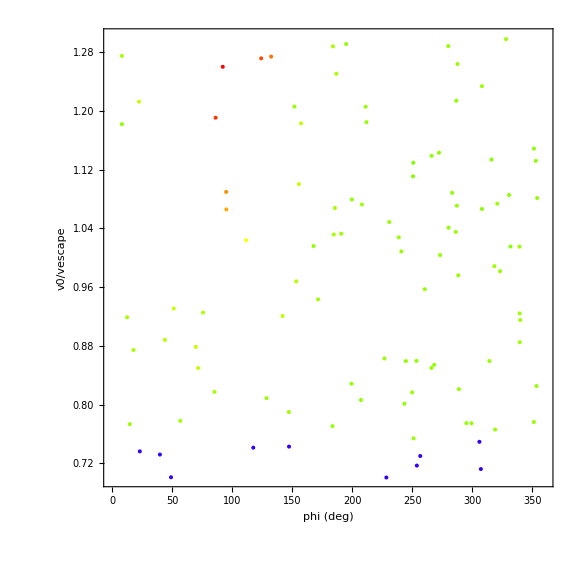

```mathematica
t1
myNmax=Length[t1];
mymin=1*10^75;
i=1;
While[i<myNmax,
If[ t1[[i,3]]<mymin,If[t1[[i,3]]>0,mymin=t1[[i,3]]]];
i=i+1]
mymax=Max[Table[t1[[i,3]],{i,1,myNmax}]];
range=mymax-mymin;
(* Make the final table with the color code for the final distance as the last element. *)
t2=Table[
{t1[[i,1]],
t1[[i,2]],
If[t1[[i,3]]<0,If[t1[[i,3]]==-1,0.9,0.7],0.25*(1-((t1[[i,3]]-mymin)/range))]},{i,1,myNmax}
];
(*Define the plotting function.Underscore means hold value until defined*)ThreeBodyScatterPlot[data_/;MatrixQ[data,NumberQ]&&(*Matrix Q elvaluates true if data is an array AND has 3 numbers in a data set*)Length[First[data]]===3,fun_,opts___]:=Show[Graphics[{PointSize[0.005],Map[{fun[Last[#]],Point[Take[#,2]]}&,data]},opts]]

(*Make the plot.*)p5=ThreeBodyScatterPlot[t2,Hue[#,1,If[#==0.9,0,1]]&,(*applies color according to hitting the sun,earth or inbetween*)Axes->True,AxesLabel->{"x","y","z"},AspectRatio->1,Frame->True,PlotRange->{{0,360},{0.7,1.3}},BaseStyle->FontSize->16,ImageSize->8*72,Frame->True,FrameLabel->{"phi (deg)","v0/vescape"}]
```

```mathematica
Export["C:\\Users\\Omair\\Desktop\\out2.dat",t1];
```